# Transient

```mathematica
r1=6; r2=30;r3=0;
γ1=6.6;
kfp0=29.1*10^-3; kfm=8.1*10^-5;kcp0=12.8*10^-3; kcm=2*10^-4; kpp0=10^-5; kpm=0.187; 

Id=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}});  
km[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_]:=({{-(kfp0*F+kcp0*CP+kpp0*P), kfm, kcm, kpm}, {kfp0*F, -kfm, 0, 0}, {kcp0*CP, 0, -kcm, 0}, {kpp0*P, 0, 0, -kpm}})
Iv=({{1}, {0}, {0}, {0}}); 
Ret[r1_,r2_,r3_,γ1_]:=({{r1, 0, 0, 0}, {0, r2, 0, 0}, {0, 0, r3, 0}, {0, 0, 0, γ1}})
 Rem[r1_,r2_,r3_,γ1_]:=({{r1, r2, r3, γ1}})


dlsv0[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_,s_]:=(Inverse[(s*Id-km[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P])].Iv)//Chop
θu[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_,s_]:=({{dlsv0[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,s][[1,1]]}, {dlsv0[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,s][[2,1]]}, {dlsv0[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,s][[3,1]]}, {0}})
θd[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_,s_]:=({{0}, {0}, {0}, {dlsv0[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,s][[4,1]]}})


dlsv1[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_,r1_,r2_,r3_,γ1_,s_]:=(Inverse[(s*Id-km[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P])].Ret[r1,r2,r3,γ1].(θu[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,s]-θd[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,s]))//Chop
ξ1u[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_,r1_,r2_,r3_,γ1_,s_]:=({{dlsv1[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,s][[1,1]]}, {dlsv1[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,s][[2,1]]}, {dlsv1[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,s][[3,1]]}, {0}})
ξ1d[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_,r1_,r2_,r3_,γ1_,s_]:=({{0}, {0}, {0}, {dlsv1[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,s][[4,1]]}})


dlsv2[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_,r1_,r2_,r3_,γ1_,s_]:=(Inverse[(s*Id-km[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P])].Ret[r1,r2,r3,γ1].dlsv0[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,s]+2*Inverse[(s*Id-km[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P])].Ret[r1,r2,r3,γ1].(ξ1u[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,s]-ξ1d[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,s]))//Chop
ξ2u[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_,r1_,r2_,r3_,γ1_,s_]:=({{dlsv2[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,s][[1,1]]}, {dlsv2[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,s][[2,1]]}, {dlsv2[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,s][[3,1]]}, {0}})
ξ2d[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_,r1_,r2_,r3_,γ1_,s_]:=({{0}, {0}, {0}, {dlsv2[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,s][[4,1]]}})


dls[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_,r1_,r2_,r3_,γ1_,s_]:=(1/s*Rem[r1,r2,r3,γ1].(θu[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,s]-θd[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,s]))

dl2s[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_,r1_,r2_,r3_,γ1_,s_]:=(1/s*Rem[r1,r2,r3,γ1].(θu[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,s]+θd[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,s])+2/s*Rem[r1,r2,r3,γ1].(ξ1u[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,s]-ξ1d[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,s]))

dl3s[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_,r1_,r2_,r3_,γ1_,s_]:=(1/s*Rem[r1,r2,r3,γ1].(θu[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,s]-θd[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,s])+3/s*Rem[r1,r2,r3,γ1].((ξ1u[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,s]+ξ1d[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,s])+(ξ2u[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,s]-ξ2d[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,s])))

dlst0[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_,t_]:=InverseLaplaceTransform[dlsv0[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,s],s,t]
dltm[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_,r1_,r2_,r3_,γ1_,t_]:=Quiet@Chop[InverseLaplaceTransform[dls[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,s],s,t,Assumptions->{t>0,Re[s]>0}]]
dl2tm[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_,r1_,r2_,r3_,γ1_,t_]:=Quiet@Chop[InverseLaplaceTransform[dl2s[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,s],s,t,Assumptions->{t>0,Re[s]>0}]]
dl3tm[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_,r1_,r2_,r3_,γ1_,t_]:=Quiet@Chop[InverseLaplaceTransform[dl3s[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,s],s,t,Assumptions->{t>0,Re[s]>0}]]


dlt[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_,r1_,r2_,r3_,γ1_,t_]:=Abs[dltm[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,t][[1,1]]]
dlt1[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_,r1_,r2_,r3_,γ1_,t_]:=dltm[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,t][[1,1]]
dl2t[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_,r1_,r2_,r3_,γ1_,t_]:=Abs[dl2tm[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,t][[1,1]]]
dl3t[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_,r1_,r2_,r3_,γ1_,t_]:=dl3tm[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,t][[1,1]]
vt[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_,r1_,r2_,r3_,γ1_,t_]:=(dl2t[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,t]-(dlt[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,t])^2)
ft[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_,r1_,r2_,r3_,γ1_,t_]:=vt[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,t]/dlt[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,t]
cvt[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_,r1_,r2_,r3_,γ1_,t_]:=Re[Sqrt[vt[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,t]]/dlt[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,t]]
```

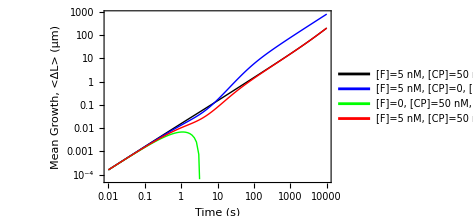

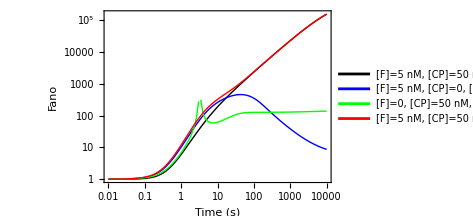

```mathematica
ti=0.01; tf=10000;

p6=LogLogPlot[{dlt1[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,50,0,r1,r2,r3,γ1,t]*0.0027,dlt1[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,0,50000,r1,r2,r3,γ1,t]*0.0027,dlt1[kfp0,kfm,kcp0,kcm,kpp0,kpm,0,50,50000,r1,r2,r3,γ1,t]*0.0027,dlt1[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,50,50000,r1,r2,r3,γ1,t]*0.0027},{t,ti,tf},Frame->{{True,False},{True,False}},GridLines->Automatic,FrameStyle->Directive[Black,Thick],PlotStyle->{{Black,Thick},{Blue,Thick},{Green,Thick},{Red,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"Time (s)","Mean Growth, <ΔL> (μm)"},ImageSize->350,PlotLegends->{"[F]=5 nM, [CP]=50 nM, [P]=0","[F]=5 nM, [CP]=0, [P]=50 μM","[F]=0, [CP]=50 nM, [P]=50 μM","[F]=5 nM, [CP]=50 nM, [P]=50 μM"},PlotPoints->100,MaxRecursion->0,PlotRange->All]

p7=LogLogPlot[{ft[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,50,0,r1,r2,r3,γ1,t],ft[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,0,50000,r1,r2,r3,γ1,t],ft[kfp0,kfm,kcp0,kcm,kpp0,kpm,0,50,50000,r1,r2,r3,γ1,t],ft[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,50,50000,r1,r2,r3,γ1,t]},{t,ti,tf},Frame->{{True,False},{True,False}},GridLines->Automatic,FrameStyle->Directive[Black,Thick],PlotStyle->{{Black,Thick},{Blue,Thick},{Green,Thick},{Red,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"Time (s)","Fano"},ImageSize->350,PlotLegends->{"[F]=5 nM, [CP]=50 nM, [P]=0","[F]=5 nM, [CP]=0, [P]=50 μM","[F]=0, [CP]=50 nM, [P]=50 μM","[F]=5 nM, [CP]=50 nM, [P]=50 μM"},PlotPoints->100,MaxRecursion->0,PlotRange->All]


(*Data Export*)
(*toEString[dat_]:=If[dat==0.,"0.0000000E+00",MantissaExponent[dat]//With[{mantissa=#[[1]],exponent=#[[2]]},{If[mantissa<0,"-",""],"0.",ToString/@PadRight[First[RealDigits[mantissa,10,Automatic]],16,0],If[exponent<0,"E-","E+"],ToString/@IntegerDigits[exponent,10,2]}//Flatten//StringJoin]&];*)




toEString[dat_,digits_:7]:=Module[{mantissa,exponent,dec},Which[Not[NumericQ[dat]],"NaN",dat==0.,"0."<>StringJoin@Table["0",{digits}]<>"E+00",True,{mantissa,exponent}=MantissaExponent[dat];
dec=IntegerPart[Abs[mantissa]*10^digits];
StringJoin@{If[mantissa<0,"-",""],"0.",StringPadLeft[ToString[dec],digits,"0"],If[exponent<0,"E-","E+"],StringPadLeft[ToString[Abs[exponent]],2,"0"]}]];




ti=0.01; 
tf3=0.1; tf4=1; tf5=10; tf6=100; tf7=1000; tf8=10000;
dt3=0.0009; dt4=0.009; dt5=0.09; dt6=0.9; dt7 = 9; dt8=90;


tb13=Table[{t,dlt1[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,50,0,r1,r2,r3,γ1,t]*0.0027,dlt1[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,0,50000,r1,r2,r3,γ1,t]*0.0027,dlt1[kfp0,kfm,kcp0,kcm,kpp0,kpm,0,50,50000,r1,r2,r3,γ1,t]*0.0027,dlt1[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,50,50000,r1,r2,r3,γ1,t]*0.0027},{t,ti,tf3,dt3}];
tb14=Table[{t,dlt1[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,50,0,r1,r2,r3,γ1,t]*0.0027,dlt1[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,0,50000,r1,r2,r3,γ1,t]*0.0027,dlt1[kfp0,kfm,kcp0,kcm,kpp0,kpm,0,50,50000,r1,r2,r3,γ1,t]*0.0027,dlt1[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,50,50000,r1,r2,r3,γ1,t]*0.0027},{t,tf3+dt4,tf4,dt4}];
tb15=Table[{t,dlt1[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,50,0,r1,r2,r3,γ1,t]*0.0027,dlt1[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,0,50000,r1,r2,r3,γ1,t]*0.0027,dlt1[kfp0,kfm,kcp0,kcm,kpp0,kpm,0,50,50000,r1,r2,r3,γ1,t]*0.0027,dlt1[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,50,50000,r1,r2,r3,γ1,t]*0.0027},{t,tf4+dt5,tf5,dt5}];
tb16=Table[{t,dlt1[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,50,0,r1,r2,r3,γ1,t]*0.0027,dlt1[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,0,50000,r1,r2,r3,γ1,t]*0.0027,dlt1[kfp0,kfm,kcp0,kcm,kpp0,kpm,0,50,50000,r1,r2,r3,γ1,t]*0.0027,dlt1[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,50,50000,r1,r2,r3,γ1,t]*0.0027},{t,tf5+dt6,tf6,dt6}];
tb17=Table[{t,dlt1[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,50,0,r1,r2,r3,γ1,t]*0.0027,dlt1[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,0,50000,r1,r2,r3,γ1,t]*0.0027,dlt1[kfp0,kfm,kcp0,kcm,kpp0,kpm,0,50,50000,r1,r2,r3,γ1,t]*0.0027,dlt1[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,50,50000,r1,r2,r3,γ1,t]*0.0027},{t,tf6+dt7,tf7,dt7}];
tb18=Table[{t,dlt1[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,50,0,r1,r2,r3,γ1,t]*0.0027,dlt1[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,0,50000,r1,r2,r3,γ1,t]*0.0027,dlt1[kfp0,kfm,kcp0,kcm,kpp0,kpm,0,50,50000,r1,r2,r3,γ1,t]*0.0027,dlt1[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,50,50000,r1,r2,r3,γ1,t]*0.0027},{t,tf7+dt8,tf8,dt8}]
tb1=N[Join[tb13,tb14,tb15,tb16,tb17,tb18]];
tbp1=StringJoin[StringJoin[toEString[#[[1]],7]<>"   "<>toEString[#[[2]],7]<>"   "<>toEString[#[[3]],7]<>"   "<>toEString[#[[4]],7]<>"   "<>toEString[#[[5]],7]<>"\n"]&/@tb1];
Export["F:\\Colab\\Sandeep\\2-Actin\\Results\\Analytics\\2plus1model\\t-dlt.dat",tbp1,"FieldSeparators"->"    "];




tb13=Table[{t,ft[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,50,0,r1,r2,r3,γ1,t],ft[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,0,50000,r1,r2,r3,γ1,t],ft[kfp0,kfm,kcp0,kcm,kpp0,kpm,0,50,50000,r1,r2,r3,γ1,t],ft[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,50,50000,r1,r2,r3,γ1,t]},{t,ti,tf3,dt3}];
tb14=Table[{t,ft[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,50,0,r1,r2,r3,γ1,t],ft[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,0,50000,r1,r2,r3,γ1,t],ft[kfp0,kfm,kcp0,kcm,kpp0,kpm,0,50,50000,r1,r2,r3,γ1,t],ft[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,50,50000,r1,r2,r3,γ1,t]},{t,tf3+dt4,tf4,dt4}];
tb15=Table[{t,ft[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,50,0,r1,r2,r3,γ1,t],ft[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,0,50000,r1,r2,r3,γ1,t],ft[kfp0,kfm,kcp0,kcm,kpp0,kpm,0,50,50000,r1,r2,r3,γ1,t],ft[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,50,50000,r1,r2,r3,γ1,t]},{t,tf4+dt5,tf5,dt5}];
tb16=Table[{t,ft[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,50,0,r1,r2,r3,γ1,t],ft[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,0,50000,r1,r2,r3,γ1,t],ft[kfp0,kfm,kcp0,kcm,kpp0,kpm,0,50,50000,r1,r2,r3,γ1,t],ft[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,50,50000,r1,r2,r3,γ1,t]},{t,tf5+dt6,tf6,dt6}];
tb17=Table[{t,ft[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,50,0,r1,r2,r3,γ1,t],ft[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,0,50000,r1,r2,r3,γ1,t],ft[kfp0,kfm,kcp0,kcm,kpp0,kpm,0,50,50000,r1,r2,r3,γ1,t],ft[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,50,50000,r1,r2,r3,γ1,t]},{t,tf6+dt7,tf7,dt7}];
tb18=Table[{t,ft[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,50,0,r1,r2,r3,γ1,t],ft[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,0,50000,r1,r2,r3,γ1,t],ft[kfp0,kfm,kcp0,kcm,kpp0,kpm,0,50,50000,r1,r2,r3,γ1,t],ft[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,50,50000,r1,r2,r3,γ1,t]},{t,tf7+dt8,tf8,dt8}];
tb1=N[Join[tb13,tb14,tb15,tb16,tb17,tb18]];
tbp1=StringJoin[StringJoin[toEString[#[[1]],7]<>"   "<>toEString[#[[2]],7]<>"   "<>toEString[#[[3]],7]<>"   "<>toEString[#[[4]],7]<>"   "<>toEString[#[[5]],7]<>"\n"]&/@tb1];
Export["F:\\Colab\\Sandeep\\2-Actin\\Results\\Analytics\\2plus1model\\t-ft.dat",tbp1,"FieldSeparators"->"    "];
```

# Long-time Limit

```mathematica
r1=6; r2=30;r3=0;
γ1=6.6;
kfp0=29.1*10^-3; kfm=8.1*10^-5;kcp0=12.8*10^-3; kcm=2*10^-4; kpp0=10^-5; kpm=0.187; 

Id=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}});  
km[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_]:=({{-(kfp0*F+kcp0*CP+kpp0*P), kfm, kcm, kpm}, {kfp0*F, -kfm, 0, 0}, {kcp0*CP, 0, -kcm, 0}, {kpp0*P, 0, 0, -kpm}})
Iv=({{1}, {0}, {0}, {0}}); 
Ret[r1_,r2_,r3_,γ1_]:=({{r1, 0, 0, 0}, {0, r2, 0, 0}, {0, 0, r3, 0}, {0, 0, 0, γ1}})
Rem[r1_,r2_,r3_,γ1_]:=({{r1, r2, r3, γ1}})


dltv01=({{p1}, {p2}, {p3}, {p4}}); Y=({{1, 1, 1, 1}});
e1[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_]:=km[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P].dltv01
e2=Y.dltv01;

eq1[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_]:=e1[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P][[1,1]]
eq2[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_]:=e1[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P][[2,1]]
eq3[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_]:=e1[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P][[3,1]]
eq4[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_]:=e1[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P][[4,1]]
eq5=e2[[1,1]];

sol[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_]:=Solve[{eq1[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P]==0,eq2[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P]==0,eq3[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P]==0,eq5==1},{p1,p2,p3,p4}]

p11[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_]:=p1/.sol[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P][[1,1]]
p12[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_]:=p2/.sol[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P][[1,2]]
p13[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_]:=p3/.sol[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P][[1,3]]
p14[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_]:=p4/.sol[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P][[1,4]]

dlsv0[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_]:=({{p11[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P]}, {p12[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P]}, {p13[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P]}, {p14[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P]}})

θu[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_]:=({{dlsv0[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P][[1,1]]}, {dlsv0[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P][[2,1]]}, {dlsv0[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P][[3,1]]}, {0}})
θd[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_]:=({{0}, {0}, {0}, {dlsv0[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P][[4,1]]}})

dlsv1[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_,r1_,r2_,r3_,γ1_,s_]:=1/s*Inverse[(s*Id-km[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P])].Ret[r1,r2,r3,γ1].(θu[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P]-θd[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P])//Chop

ξ1u[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_,r1_,r2_,r3_,γ1_,s_]:=({{dlsv1[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,s][[1,1]]}, {dlsv1[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,s][[2,1]]}, {dlsv1[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,s][[3,1]]}, {0}})
ξ1d[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_,r1_,r2_,r3_,γ1_,s_]:=({{0}, {0}, {0}, {dlsv1[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,s][[4,1]]}})

dlsv2[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_,r1_,r2_,r3_,γ1_,s_]:=1/s*Inverse[(s*Id-km[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P])].Ret[r1,r2,r3,γ1].dlsv0[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P]+2*Inverse[(s*Id-km[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P])].Ret[r1,r2,r3,γ1].(ξ1u[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,s]-ξ1d[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,s])//Chop

ξ2u[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_,r1_,r2_,r3_,γ1_,s_]:=({{dlsv2[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,s][[1,1]]}, {dlsv2[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,s][[2,1]]}, {dlsv2[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,s][[3,1]]}, {0}})
ξ2d[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_,r1_,r2_,r3_,γ1_,s_]:=({{0}, {0}, {0}, {dlsv2[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,s][[4,1]]}})

dls[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_,r1_,r2_,r3_,γ1_,s_]:=1/s^2*Rem[r1,r2,r3,γ1].(θu[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P]-θd[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P])

dl2s[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_,r1_,r2_,r3_,γ1_,s_]:=1/s^2*Rem[r1,r2,r3,γ1].(θu[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P]+θd[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P])+2/s*Rem[r1,r2,r3,γ1].(ξ1u[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,s]-ξ1d[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,s])

dl3s[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_,r1_,r2_,r3_,γ1_,s_]:=1/s^2*Rem[r1,r2,r3,γ1].(θu[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P]-θd[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P])+3/s*Rem[r1,r2,r3,γ1].((ξ1u[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,s]+ξ1d[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,s])+(ξ2u[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,s]-ξ2d[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,s]))

dltm[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_,r1_,r2_,r3_,γ1_,t_]:=Quiet@Chop[InverseLaplaceTransform[dls[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,s],s,t,Assumptions->{t>0,Re[s]>0}]]
dl2tm[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_,r1_,r2_,r3_,γ1_,t_]:=Quiet@Chop[InverseLaplaceTransform[dl2s[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,s],s,t,Assumptions->{t>0,Re[s]>0}]]
dl3tm[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_,r1_,r2_,r3_,γ1_,t_]:=Quiet@Chop[InverseLaplaceTransform[dl3s[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,s],s,t,Assumptions->{t>0,Re[s]>0}]]

dlt[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_,r1_,r2_,r3_,γ1_,t_]:=Abs[dltm[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,t][[1,1]]]
dlt1[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_,r1_,r2_,r3_,γ1_,t_]:=dltm[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,t][[1,1]]
dl2t[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_,r1_,r2_,r3_,γ1_,t_]:=Abs[dl2tm[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,t][[1,1]]]
dl3t[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_,r1_,r2_,r3_,γ1_,t_]:=dl3tm[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,t][[1,1]]
vt[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_,r1_,r2_,r3_,γ1_,t_]:=(dl2t[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,t]-(dlt[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,t])^2)
ft[kfp0_,kfm_,kcp0_,kcm_,kpp0_,kpm_,F_,CP_,P_,r1_,r2_,r3_,γ1_,t_]:=(vt[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,t]/dlt[kfp0,kfm,kcp0,kcm,kpp0,kpm,F,CP,P,r1,r2,r3,γ1,t])
```

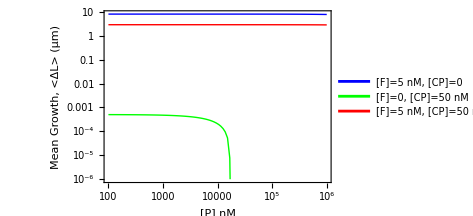

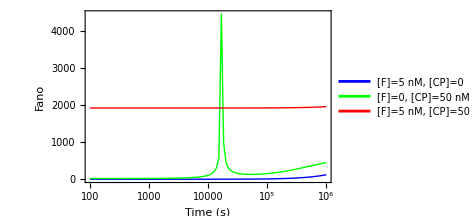

```mathematica
Pin=100; Pf=1000000;

p6=LogLogPlot[{dlt1[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,0,P,r1,r2,r3,γ1,100]*0.0027,dlt1[kfp0,kfm,kcp0,kcm,kpp0,kpm,0,50,P,r1,r2,r3,γ1,100]*0.0027,dlt1[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,50,P,r1,r2,r3,γ1,100]*0.0027},{P,Pin,Pf},Frame->{{True,False},{True,False}},GridLines->Automatic,FrameStyle->Directive[Black,Thick],PlotStyle->{{Blue,Thick},{Green,Thick},{Red,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"[P] nM","Mean Growth, <ΔL> (μm)"},ImageSize->350,PlotLegends->{"[F]=5 nM, [CP]=0","[F]=0, [CP]=50 nM","[F]=5 nM, [CP]=50 nM"},PlotPoints->100,MaxRecursion->0,PlotRange->All]

p7=LogLinearPlot[{ft[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,0,P,r1,r2,r3,γ1,100],ft[kfp0,kfm,kcp0,kcm,kpp0,kpm,0,50,P,r1,r2,r3,γ1,100],ft[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,50,P,r1,r2,r3,γ1,100]},{P,Pin,Pf},Frame->{{True,False},{True,False}},GridLines->Automatic,FrameStyle->Directive[Black,Thick],PlotStyle->{{Blue,Thick},{Green,Thick},{Red,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"Time (s)","Fano"},ImageSize->350,PlotLegends->{"[F]=5 nM, [CP]=0","[F]=0, [CP]=50 nM","[F]=5 nM, [CP]=50 nM"},PlotPoints->100,MaxRecursion->0,PlotRange->All]


toEString[dat_,digits_:7]:=Module[{mantissa,exponent,dec},Which[Not[NumericQ[dat]],"NaN",dat==0.,"0."<>StringJoin@Table["0",{digits}]<>"E+00",True,{mantissa,exponent}=MantissaExponent[dat];
dec=IntegerPart[Abs[mantissa]*10^digits];
StringJoin@{If[mantissa<0,"-",""],"0.",StringPadLeft[ToString[dec],digits,"0"],If[exponent<0,"E-","E+"],StringPadLeft[ToString[Abs[exponent]],2,"0"]}]];


Pin=100; 
Pf3=1000; Pf4=10000; Pf5=100000; Pf6=1000000; 
dt3=9; dt4=90; dt5=900; dt6=9000;


tb13=Table[{P,dlt1[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,0,P,r1,r2,r3,γ1,100]*0.0027,dlt1[kfp0,kfm,kcp0,kcm,kpp0,kpm,0,50,P,r1,r2,r3,γ1,100]*0.0027,dlt1[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,50,P,r1,r2,r3,γ1,100]*0.0027},{P,Pin,Pf3,dt3}];
tb14=Table[{P,dlt1[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,0,P,r1,r2,r3,γ1,100]*0.0027,dlt1[kfp0,kfm,kcp0,kcm,kpp0,kpm,0,50,P,r1,r2,r3,γ1,100]*0.0027,dlt1[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,50,P,r1,r2,r3,γ1,100]*0.0027},{P,Pf3+dt4,Pf4,dt4}];
tb15=Table[{P,dlt1[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,0,P,r1,r2,r3,γ1,100]*0.0027,dlt1[kfp0,kfm,kcp0,kcm,kpp0,kpm,0,50,P,r1,r2,r3,γ1,100]*0.0027,dlt1[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,50,P,r1,r2,r3,γ1,100]*0.0027},{P,Pf4+dt5,Pf5,dt5}];
tb16=Table[{P,dlt1[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,0,P,r1,r2,r3,γ1,100]*0.0027,dlt1[kfp0,kfm,kcp0,kcm,kpp0,kpm,0,50,P,r1,r2,r3,γ1,100]*0.0027,dlt1[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,50,P,r1,r2,r3,γ1,100]*0.0027},{P,Pf5+dt6,Pf6,dt6}];
tb1=N[Join[tb13,tb14,tb15,tb16]];
tbp1=StringJoin[StringJoin[toEString[#[[1]],7]<>"   "<>toEString[#[[2]],7]<>"   "<>toEString[#[[3]],7]<>"   "<>toEString[#[[4]],7]<>"\n"]&/@tb1];
Export["F:\\Colab\\Sandeep\\2-Actin\\Results\\Analytics\\2plus1model\\P-dlt.dat",tbp1,"FieldSeparators"->"    "];




tb13=Table[{P,ft[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,0,P,r1,r2,r3,γ1,100],ft[kfp0,kfm,kcp0,kcm,kpp0,kpm,0,50,P,r1,r2,r3,γ1,100],ft[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,50,P,r1,r2,r3,γ1,100]},{P,Pin,Pf3,dt3}];
tb14=Table[{P,ft[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,0,P,r1,r2,r3,γ1,100],ft[kfp0,kfm,kcp0,kcm,kpp0,kpm,0,50,P,r1,r2,r3,γ1,100],ft[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,50,P,r1,r2,r3,γ1,100]},{P,Pf3+dt4,Pf4,dt4}];
tb15=Table[{P,ft[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,0,P,r1,r2,r3,γ1,100],ft[kfp0,kfm,kcp0,kcm,kpp0,kpm,0,50,P,r1,r2,r3,γ1,100],ft[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,50,P,r1,r2,r3,γ1,100]},{P,Pf4+dt5,Pf5,dt5}];
tb16=Table[{P,ft[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,0,P,r1,r2,r3,γ1,100],ft[kfp0,kfm,kcp0,kcm,kpp0,kpm,0,50,P,r1,r2,r3,γ1,100],ft[kfp0,kfm,kcp0,kcm,kpp0,kpm,5,50,P,r1,r2,r3,γ1,100]},{P,Pf5+dt6,Pf6,dt6}];
tb1=N[Join[tb13,tb14,tb15,tb16]];
tbp1=StringJoin[StringJoin[toEString[#[[1]],7]<>"   "<>toEString[#[[2]],7]<>"   "<>toEString[#[[3]],7]<>"   "<>toEString[#[[4]],7]<>"\n"]&/@tb1];
Export["F:\\Colab\\Sandeep\\2-Actin\\Results\\Analytics\\2plus1model\\P-ft.dat",tbp1,"FieldSeparators"->"    "];
```